22,46,78,118

```mathematica
f[x_,y_,z_,n_]:=2*((x*y+x*z+y*z)+2(n-1)(x+y+z)+2(n-2)(n-1))
```

```mathematica
f[11,1,1,1]
```

46

```mathematica
Table[f[2,4,6,x],{x,1,20}]
```

{88,136,192,256,328,408,496,592,696,808,928,1056,1192,1336,1488,1648,1816,1992,2176,2368}

```mathematica
nvals=Sort[Flatten[Table[f[a,b,c,x],{a,1,20},{b,1,20},{c,1,20},{x,1,5}]]]
```

{6,10,10,10,14,14,14,16,16,16,18,18,18,18,22,22,22,22,22,22,22,22,22,24,26,26,26,26,26,26,28,28,28,28,28,28,30,30,30,30,30,30,32,32,32,34,34,39906,2944,2944,2960,2960,2960,2962,2962,2962,3024,3024,3024,3030,3030,3030,3030,3030,3030,3032,3032,3032,3034,3034,3034,3052,3052,3052,3120,3120,3120,3124,3124,3124,3124,3124,3124,3126,3144,3216,3216,3216,3218,3218,3218,3312,3312,3312,3408}
 |  |  |  |

```mathematica
Length[Select[nvals,#==30&]]
```

6

```mathematica
Plot[2(a*b+a*c+b*c)<154,{a,b,c},Integers]
```

Plot::nonopt: Options expected (instead of Integers) beyond position 2 in Plot[2 (a b+a c+b c)<154,{a,b,c},Integers]. An option must be a rule or a list of rules.

```mathematica
Plot[2 (a b+a c+b c)<154,{a,b,c}]
```

Plot::plln: Limiting value b in {a,b,c} is not a machine-sized real number.

Plot[2 (a b+a c+b c)<154,{a,b,c}]

```mathematica
a=.
b=.
c=.
Plot3D[2 (a* b+a* c+b* c)<154]
```

Plot3D::argtu: Plot3D called with 1 argument; 2 or 3 arguments are expected.

Plot3D[2 (a b+a c+b c)<154]

```mathematica
RegionPlot3D[2 (a* b+a* c+b* c)<1000000 &&0<a≤b≤c,{a,0,1000},{b,0,2000},{c,0,4000}]
```

-Graphics3D-

```mathematica
RegionPlot3D[2 (a* b+a* c+b* c)<154 &&0<a≤b≤c,PlotRange->Full]
```

RegionPlot3D::invplotreg: {2 (a b+a c+b c)<154&&0<a≤b≤c} is not a valid region to plot.

RegionPlot3D[2 (a b+a c+b c)<154&&0<a≤b≤c,PlotRange→Full]

```mathematica
a=.;b=.;c=.
```

```mathematica
FindInstance[a*b+a*c+b*c==47 && a+b+c==12 &&0<{a,b,c},{a,b,c},Integers,10]
```

{{a→3,b→4,c→5},{a→3,b→5,c→4},{a→4,b→3,c→5},{a→4,b→5,c→3},{a→5,b→3,c→4},{a→5,b→4,c→3}}

6,10,14,16,18,22,24,26,28,30,32,34,38,40,42

WolframAlphaQueryResults

```mathematica
{a,b,c}=.
```

{Null,Null,Null}

```mathematica
FindInstance[a*b+a*c+b*c==143 && 0<a<=b<=c,{a,b,c},Integers,20]
```

{{a→1,b→1,c→71},{a→1,b→2,c→47},{a→1,b→3,c→35},{a→1,b→5,c→23},{a→1,b→7,c→17},{a→1,b→8,c→15},{a→1,b→11,c→11},{a→2,b→5,c→19},{a→3,b→5,c→16},{a→5,b→7,c→9}}

-66.2992+17.8238 x

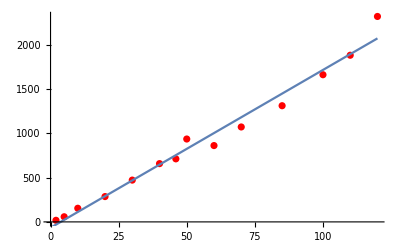

```mathematica
Cn={{2,18},{5,58},{10,154},{20,286},{30,472},{40,658},{46,712},{50,936},{60,862},{70,1072},{85,1312},{100,1662},{110,1882},{120,2320}};
line=Fit[Cn,{1,x},x]
Show[ListPlot[Cn,PlotStyle->Red],Plot[line,{x,0,120}]]
```

```mathematica
71*71
```

5041

```mathematica
Mod[5041,107]
```

12

```mathematica
FindInstance[240+16x==a*b && 0<x && a+b==32,{x,a,b},Integers,20]
```

{{x→1,a→16,b→16}}